# Cluster evolution in Antonini and Gieles 2020

This notebook is based entirely on the work of Antonini and Gieles (2020) Monthly Notices of the Royal Astronomical Society 492, 2936. doi:10.1093/mnras/stz3584 (“AG2020”).

This notebook is broken up into two parts:

The first (1.) is their model for the “background” evolution of the cluster, which includes changes in the half light radius, the masses of the BH and non BH populations etc. i.e. at the population scale. This model is determined directly from NBODY simulations and matches remarkably well for different properties (e.g. total N) spanning many orders of magnitude. 

Try changing NBH or nstar and to solve for properties of the cluster until t_end.

The second (2.) models the “foreground” evolution of the black hole mergers, given the time evolution of the cluster properties. The integrals used (derived in AG2020) rely on several simplifying assumptions, such as that all black holes involved in hardening interactions are equal mass. For a given model in (1.), the merger rates from three mechanisms (GW only, GW resonant capture, GW out of cluster) are calculated.

## 1. Evolving cluster mass and radius (“GCBH”)

This section covers the relaxation of the cluster. It is referred to as GCBH. 
The mass loss is driven by both stellar evolution and dynamical interactions. All of this important physics is contained in the fitting parameters. Half light radius evolution driven by relaxation process -> mass segregation (also from fitting) 
Nothing about mergers implied here yet.

### Solving the DEs: GCBH

ζ, β, ν and a_1 are found in the paper by fitting to NBODY models, after fixing t_sev

```mathematica
ζ = 0.1;
NBH = 1000;
β = 0.00241;
Nrh = 3.48;
Myr = 10^6 π 10^7;
Gyr = 10^9 π 10^7;
tsev = 2Myr;
ν = 0.0808;
a1 = 1.76;
pc = 3.018 10^18;
G = 6.67 10^-8;
c = 3 10^10;
Msol = 2 10^33;
m1 =10 Msol;
m2 =10 Msol;
m3 =10 Msol;
m12 = m1+m2;
m123=m1+m2+m3;
mbh = NBH m1;
nstar = 2 10^5;
mstar = nstar 1 Msol;
Rs = (G m12)/c^2;
rh0 = 2 pc;
tend = 44000 Myr;
tstart = 10;
kms = 10^5;
NstarBH = nstar + NBH;
```

```mathematica
trh0 = 0.138((mbh+mstar)rh0^3/G)^(1/2)1/((mbh+mstar)/NstarBH(1+a1 (mbh/(mbh+mstar))/0.01)10)
tcc = Nrh trh0
```

4.21627×10^15

1.46726×10^16

```mathematica
trh0/Gyr
tcc/Gyr
```

0.134208

0.467044

```mathematica
N[tsev]
```

6.28319×10^13

```mathematica
trh1[t_] = 0.138((MBH[t]+Mstar[t])rh[t]^3/G)^(1/2)1/((MBH[t]+Mstar[t])/NstarBH(1+a1 (MBH[t]/(MBH[t]+Mstar[t]))/0.01)10);
```

```mathematica
Systemc = {MBH'[t]== Piecewise[{{0,t<tcc},{-β (MBH[t]+Mstar[t])/trh1[t],t>tcc &&MBH[t]>0},{0,t>tcc &&MBH[t]<0}}],
Mstar'[t]== Piecewise[{{0,t<tsev},{-ν Mstar[t]/t,t>tsev}}] ,
rh'[t] == Piecewise[{{0,0<t<tsev},{ν (Mstar[t]/t)/(MBH[t]+Mstar[t])rh[t],tsev<t<tcc},{ζ rh[t]/trh1[t]+ 2(-ν Mstar[t]/t -β (Mstar[t]+MBH[t])/trh1[t])/(MBH[t]+Mstar[t])rh[t],t>tcc}}],
MBH[10]==mbh,Mstar[10]== mstar,rh[10]==rh0};
solc=NDSolve[Systemc,{MBH,Mstar,rh},{t,0.1,tend}];
```

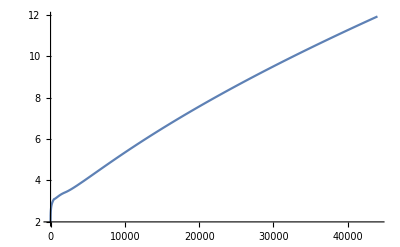

```mathematica
Plot[rh[t Myr]/pc/.solc,{t,0.1,tend/Myr}]
```

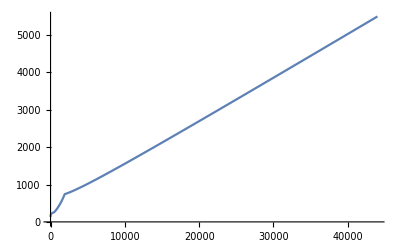

```mathematica
Plot[trh1[t Myr]/Myr/.solc,{t,0.1,tend/Myr}]
```

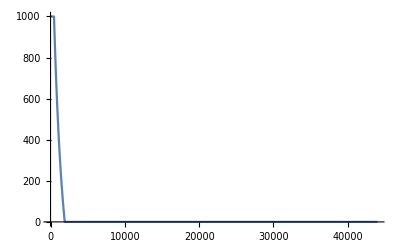

```mathematica
Plot[MBH[t Myr]/Msol/.solc,{t,0.1,tend/Myr}]
```

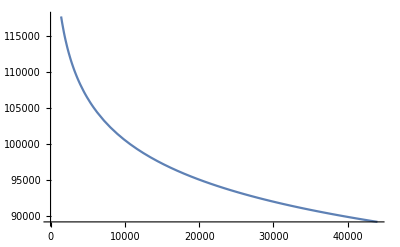

```mathematica
Plot[Mstar[t Myr]/Msol/.solc,{t,0.1,tend/Myr}]
```

## 2. Putting BH mergers on top (“BHDYN”)

Here we will determine the number of mergers in each of the three categories (in cluster, resonant, outside of cluster) and with this determine the eccentricity. We get out i) rates and ii) eccentricity with the following:
We can take the output of GCBH

Are they tuning anything like the previous model? Or does everything fall into place with estimates from the literature? Is this dependence weak/strong?

### Merger rates

Here we use the probability of each type of merger, given our cluster property output. Integrate over 12Gyr like in the paper.

```mathematica
Mcl[t_] = (MBH[t]+Mstar[t])/.solc;
```

```mathematica
Plot[Mcl[t]/(10^5 Msol)/.solc,{t,0,tend/1000}]
```

-Graphics-

```mathematica
dEbin[t_] = ζ (0.2 G Mcl[t]^2 /.solc)/((rh[t] trh1[t])/.solc);
```

#### In cluster, GW only

```mathematica
ϵ = 0.8;
```

```mathematica
fc = 1;
q3 = m3/m12;
```

```mathematica
lGW [a_,t_]= 1.3 ((G^4(m1 m2)^2 m12)/(c^5 dEbin[t]/.solc))^(1/7)a^(-5/7);
```

```mathematica
aGW[t_] = 1.1(1-ϵ)^(-7/10)((G^4(m1 m2)^2 m12)/(c^5 dEbin[t]/.solc))^(1/5);
vesc[t_] = 50 kms ((Mcl[t]/.solc)/(10^5 Msol))^(1/3)((3 Mcl[t] pc^3)/(8 π (rh[t]/.solc)^3 10^5 Msol))^(1/6)(fc)/.solc;
aej[t_] = (1/ϵ-1)G (m1 m2)/m123 q3/(vesc[t]/.solc)^2/.solc;
ahard[t_] =5 aej[t]/.solc;
am[t_] = Max[aGW[t]/.solc,aej[t]/.solc]/.solc;
```

```mathematica
Plot[vesc[t]/kms/.solc,{t,0,tend/1000}]
```

-Graphics-

```mathematica
Plot[((3 Mcl[t]/(Msol))/(8 π ((rh[t]/pc)/.solc)^3))/.solc,{t,0,tend}]
```

-Graphics-

```mathematica
mej[t_]= m12+m3/(1-ϵ)Log[(aej[t]/.solc)/(am[t]/.solc)q3^-2]/.solc;
```

```mathematica
Γbin[t_] = -(MBH'[t]/.solc)/(mej[t]/.solc);
```

```mathematica
Pin[t_]= 7/10 1/(1-ϵ)(lGW[am[t],t]/.solc)^2;
Nin = Flatten[NIntegrate[Γbin[t] Pin[t],{t,tstart,tend}],5]
```

{{{0.481542}}}

#### In cluster, GW resonant capture

```mathematica
NIS = 20;
h=1.8;
```

```mathematica
gcap = h^2 Rs^(5/7);
gGW[t_] = 1.7((G^4(m1 m2)^2 m12)/(c^5 dEbin[t]/.solc))^(2/7);
aGW[t_] = (((NIS^2 gcap^2+10/7(1-ϵ)gGW[t])^(1/2)-NIS gcap)/gGW[t])^(-7/5);
am[t_] = Max[aGW[t]/.solc,aej[t]/.solc];
```

```mathematica
lcap[a_,t_] = h (Rs/am[t])^(5/14);
Pcap[t_] = NIS 7/5 1/(1-ϵ) (lcap[am[t],t]/.solc)^2 ;
mej[t_]= m12+m3/(1-ϵ)Log[aej[t]/am[t] q3^-2];
Γbin[t_] = -(MBH'[t]/.solc)/(mej[t]/.solc);
Nres = Flatten[NIntegrate[Γbin[t]Pcap[t],{t,tstart,tend}],5]
```

{0.0971563}

#### Out of cluster, GW only

```mathematica
lH[a_,τ_]=1.8((G^3 m1 m2 m12)/c^5 τ)^(1/7)a^(-4/7);

pex[t_]=lH[aej[t],t]^2 ;
Pex[t_]=(1-Pin[t]/.solc)pex[t]/.solc;
```

```mathematica
Nout = Flatten[NIntegrate[Γbin[t]Pex[t] ,{t,tstart,tend}],5]
```

{{0.470807}}